# Figure 8

#### Data

```mathematica
data1=Import["/home/daniel/Documents/Codigos/RabiModel/src/output/fidelities_ramp.dat"];
data2=Import["/home/daniel/Documents/Codigos/RabiModel/src/output/qfi_ramp.dat"];
data3=Import["/home/daniel/Documents/Codigos/RabiModel/src/output/negativity_ramp.dat"];
```

```mathematica
dat1=Table[{data1[[i,1]],data1[[i,2]]-0.004},{i,2,Length[data1]}];
dat2=Table[{data1[[i,1]],data1[[i,3]]-0.0004},{i,2,Length[data1]}];
dat3=Table[{data2[[i,1]],data2[[i,2]]},{i,1,Length[data2]}];
dat4=Table[{data2[[i,1]],data2[[i,3]]},{i,1,Length[data2]}];
dat5=Table[{data3[[i,1]],data3[[i,2]]},{i,1,Length[data3]}];
NC=80;
τ=8.2;
```

#### Figure 7d

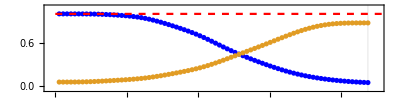

```mathematica
fig7d=Show[ListPlot[{dat1,dat2},Joined->False,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{-10,NC*τ+20},{-0.05,1.1}},GridLines->{{NC*τ},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[1,{x,0,1100},PlotStyle->{Red,Dashed}],AspectRatio->0.25]
```

#### Figure 7e

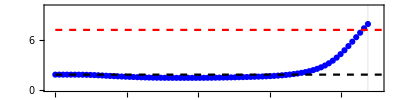

```mathematica
fig7e=Show[ListPlot[{dat3},Joined->False,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{-10,NC*τ+20},{0,10}},GridLines->{{NC*τ},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[1.8283437968627987,{x,0,1100},PlotStyle->{Black,Dashed}],Plot[7.206369005972,{x,0,1100},PlotStyle->{Red,Dashed}],AspectRatio->0.25]
```

#### Figure 7f

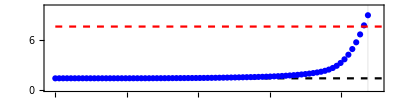

```mathematica
fig7f=Show[ListPlot[{dat4},Joined->False,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{-10,NC*τ+20},{0,10}},GridLines->{{NC*τ},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[7.607438739421753,{x,0,1100},PlotStyle->{Red,Dashed}],Plot[1.3821,{x,0,1100},PlotStyle->{Black,Dashed}],AspectRatio->0.25]
```

#### Figure 7g

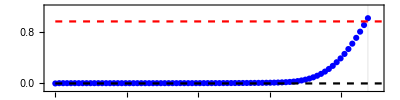

```mathematica
fig7g=Show[ListPlot[{dat5},Joined->False,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{-10,NC*τ+20},{-0.1,1.2}},GridLines->{{NC*τ},{}},Axes->False,GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[0,{x,0,1100},PlotStyle->{Black,Dashed}],Plot[0.9691210982072214,{x,0,1100},PlotStyle->{Red,Dashed}],AspectRatio->0.25]
```